# Model parameters and spectrum:

## Conventions and BZ:

Bravais basis and nearest-neighbor vector (note I am using a rotated lattice here):

```mathematica
a1={Cos[π/6],Sin[π/6]}
a2={Cos[π/6],-Sin[π/6]}

η1=a1;
η2=a2;
η3=a1-a2
```

{(√3)/2,1/2}

{(√3)/2,-1/2}

{0,1}

Reciprocal lattice vectors:

```mathematica
b1=2π *(RotationMatrix[π/2].a2)/(a1.RotationMatrix[π/2].a2)
b2=2π *(RotationMatrix[π/2].a1)/(a2.RotationMatrix[π/2].a1)
{a1.b1,a2.b2,a1.b2,a2.b1}
```

{(2 π)/(√3),2 π}

{(2 π)/(√3),-2 π}

{2 π,2 π,0,0}

And the first Brillouin zone (black) together with the path (blue) we will investigate the spectrum on:

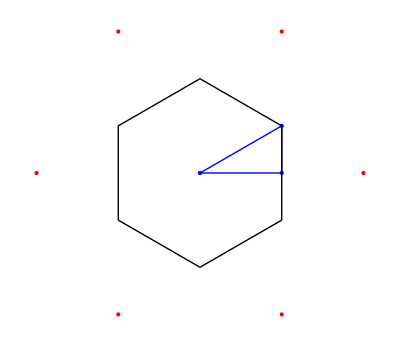

```mathematica
Dir=b1+(b1+b2);
C1=Norm[b1]/(2Cos[π/6])*Dir/Norm[Dir];
Γp={0,0};
Mp={C1[[1]],0};
Kp=C1;
Show[Graphics[{Red,PointSize[Large],Point[{b1,{0,0},b2,-b2,-b1,b1+b2,-(b1+b2)}]}],Graphics[{Blue,PointSize[Large],Point[{Γp,Mp,Kp}],Thick,Line[{Γp,Mp,Kp,Γp}]}],Graphics[{Thick,Line[Table[RotationMatrix[n π/3].C1,{n,0,6}]]}]]
```

## Setup the Hamiltonian

First we need a (generalized) Haldane for each of the two orbitals:

As always, we set t1=1.

```mathematica
HalHam[kx_,ky_]=(PauliMatrix[1]+Re[Exp[I {kx,ky}.a1]] PauliMatrix[1]-Im[Exp[I {kx,ky}.a1]] PauliMatrix[2]+Re[Exp[I {kx,ky}.a2]] PauliMatrix[1]-Im[Exp[I {kx,ky}.a2]] PauliMatrix[2])+t2 DiagonalMatrix[{Cos[{kx,ky}.a2-α2]+Cos[{kx,ky}.η3-α2]+Cos[{kx,ky}.a1+α2],Cos[{kx,ky}.a2+α2]+Cos[{kx,ky}.η3+α2]+Cos[{kx,ky}.a1-α2]}]+Δ PauliMatrix[3]+t3(PauliMatrix[1]Re[Exp[-I ({kx,ky}.(-η3)+α3)]]-PauliMatrix[2]Im[Exp[-I ({kx,ky}.(-η3)+α3)]]+PauliMatrix[1]Re[Exp[-I ({kx,ky}.(-a2-a1)+α3)]]-PauliMatrix[2]Im[Exp[-I ({kx,ky}.(-a2-a1)+α3)]]+PauliMatrix[1]Re[Exp[-I ({kx,ky}.(η3)+α3)]]-PauliMatrix[2]Im[Exp[-I ({kx,ky}.(η3)+α3)]])//ComplexExpand//FullSimplify;
HalHam[kx,ky]//MatrixForm
```

(Δ+t2 (Cos[α2+{kx,ky}.a1]+Cos[α2-{kx,ky}.a2]+Cos[α2-{kx,ky}.η3]) | 1+ⅇ^(ⅈ {kx,ky}.a1)+ⅇ^(ⅈ {kx,ky}.a2)+ⅇ^(-ⅈ (α3+{kx,ky}.(-a1-a2))) t3+ⅇ^(-ⅈ (α3+{kx,ky}.(-η3))) t3+ⅇ^(-ⅈ (α3+{kx,ky}.η3)) t3
1+ⅇ^(-ⅈ {kx,ky}.a1)+ⅇ^(-ⅈ {kx,ky}.a2)+ⅇ^(ⅈ (α3+{kx,ky}.(-a1-a2))) t3+ⅇ^(ⅈ (α3+{kx,ky}.(-η3))) t3+ⅇ^(ⅈ (α3+{kx,ky}.η3)) t3 | -Δ+t2 (Cos[α2-{kx,ky}.a1]+Cos[α2+{kx,ky}.a2]+Cos[α2+{kx,ky}.η3]))

At the K points, we have:

```mathematica
HalHam[Kp[[1]],Kp[[2]]]//FullSimplify//MatrixForm
HalHam[-Kp[[1]],-Kp[[2]]]//FullSimplify//MatrixForm
```

(Δ+3/2 t2 (-Cos[α2]+√3 Sin[α2]) | 0
0 | -Δ-3/2 t2 (Cos[α2]+√3 Sin[α2]))

(Δ-3/2 t2 (Cos[α2]+√3 Sin[α2]) | 0
0 | 1/2 (-2 Δ-3 t2 Cos[α2]+3 √3 t2 Sin[α2]))

Let’s look quickly at its spectrum:

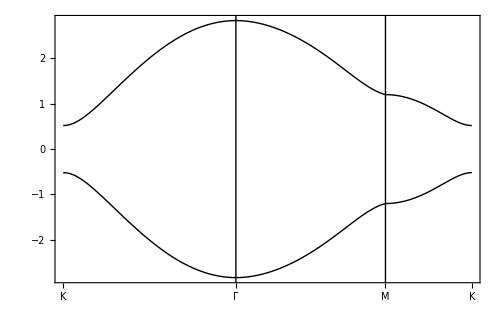
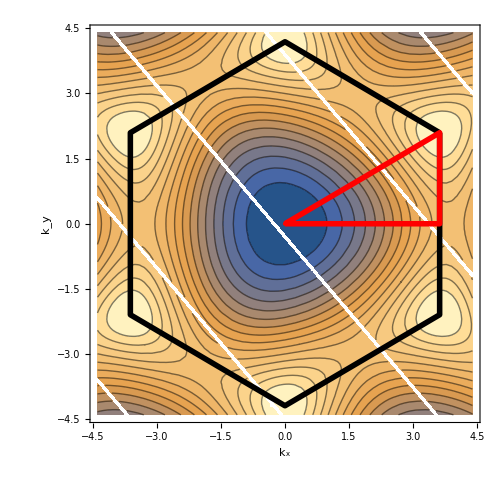

```mathematica
EVS[kx_,ky_]:=Sort[Chop[Eigenvalues[HalHam[kx,ky]/.{t2->0.2,Δ->0,α2->π/2,t3->-0.1,α3->0.3π}]]]

Δk=0.2;
Len1=Norm[Γp-Kp];
Len2=Norm[Mp-Γp];
Len3=Norm[Kp-Mp];

Ls=Table[Join[Table[{t Len1,Chop[EVS[(Kp+(Γp-Kp)*t)[[1]],(Kp+(Γp-Kp)*t)[[2]]][[band]]]},{t,0,1,0.01}],Table[{Len1+t Len2,Chop[EVS[(Γp+(Mp-Γp)*t)[[1]],(Γp+(Mp-Γp)*t)[[2]]][[band]]]},{t,0,1,0.01}],Table[{Len1+Len2+t Len3,Chop[EVS[(Mp+(Kp-Mp)*t)[[1]],(Mp+(Kp-Mp)*t)[[2]]][[band]]]},{t,0,1,0.01}]],{band,1,2}];

BAND=1;
Scl=1.4;

{Show[ListPlot[Ls,PlotMarkers->None,Joined->True,PlotStyle->{Directive[Thick,Black],Directive[Thick,Black],Directive[Thick,Red],Directive[Thick,Red]},Frame->True,FrameStyle->Thick,ImageSize->500,FrameTicksStyle->32,FrameTicks->{{Automatic,None},{{{0,"K"},{Len1,"Γ"},{Len1+Len2,"M"},{Len1+Len2+Len3,"K"}},None}}],Graphics[{Line[{{Len1,-5},{Len1,5}}],Line[{{Len1+Len2,-5},{Len1+Len2,5}}]}]],
Show[ContourPlot[EVS[kx,ky][[BAND]],{kx,-Scl π,Scl π},{ky,-Scl π,Scl π},PlotRange->Full,Contours->15,FrameStyle->Thick,FrameTicksStyle->32,FrameLabel->{"k_x","k_y"},PlotPoints->10,LabelStyle->32,ImageSize->500],Graphics[{Thickness[0.008],Line[Table[RotationMatrix[n π/3].C1,{n,0,6}]],Red,PointSize[Large],Point[{Γp,Mp,Kp}],Thickness[0.008],Line[{Γp,Mp,Kp,Γp}]}]]}
```

### Now we take two θC_2-related copies of the model (corresponds to the “two orbitals”) and couple them:

```mathematica
HalHam2[kx,ky]=HalHam[kx,ky]/.{Δ->-Δ,α2->-α2};
NNf[kx_,ky_]=1+2 ⅇ^(1/2 ⅈ √3 kx) Cos[ky/2]; 
Clear[HamFull]
HamFull[kx_,ky_]={{HalHam[kx,ky][[1]][[1]],HalHam[kx,ky][[1]][[2]],w1 Exp[I θw],w2 NNf[kx,ky]},{HalHam[kx,ky][[2]][[1]],HalHam[kx,ky][[2]][[2]],w2 NNf[-kx,ky],w1 Exp[I θw]},{w1 Exp[-I θw],w2 NNf[kx,ky],HalHam2[kx,ky][[1]][[1]],HalHam2[kx,ky][[1]][[2]]},{w2 NNf[-kx,ky],w1 Exp[-I θw],HalHam2[kx,ky][[2]][[1]],HalHam2[kx,ky][[2]][[2]]}};
HamFull[kx,ky]//MatrixForm
```

(Δ+t2 (Cos[1/2 (√3 kx-ky-2 α2)]+Cos[ky-α2]+Cos[1/2 (√3 kx+ky+2 α2)]) | ⅇ^(-ⅈ (ky+α3)) (ⅇ^(ⅈ (ky+α3))+ⅇ^(1/2 ⅈ (√3 kx+ky+2 α3)) (1+ⅇ^(ⅈ ky))+t3+ⅇ^(2 ⅈ ky) t3+ⅇ^(ⅈ (√3 kx+ky)) t3) | ⅇ^(ⅈ θw) w1 | w2 (1+2 ⅇ^(1/2 ⅈ √3 kx) Cos[ky/2])
1+ⅇ^(-1/2 ⅈ (√3 kx+ky)) (1+ⅇ^(ⅈ ky))+ⅇ^(ⅈ α3) t3 (Cos[√3 kx]+2 Cos[ky]-ⅈ Sin[√3 kx]) | -Δ+t2 (Cos[1/2 (√3 kx+ky-2 α2)]+Cos[(√3 kx)/2-ky/2+α2]+Cos[ky+α2]) | w2 (1+2 ⅇ^(-1/2 ⅈ √3 kx) Cos[ky/2]) | ⅇ^(ⅈ θw) w1
ⅇ^(-ⅈ θw) w1 | w2 (1+2 ⅇ^(1/2 ⅈ √3 kx) Cos[ky/2]) | -Δ+t2 (Cos[1/2 (√3 kx+ky-2 α2)]+Cos[ky+α2]+Cos[1/2 (√3 kx-ky+2 α2)]) | ⅇ^(-ⅈ (ky+α3)) (ⅇ^(ⅈ (ky+α3))+ⅇ^(1/2 ⅈ (√3 kx+ky+2 α3)) (1+ⅇ^(ⅈ ky))+t3+ⅇ^(2 ⅈ ky) t3+ⅇ^(ⅈ (√3 kx+ky)) t3)
w2 (1+2 ⅇ^(-1/2 ⅈ √3 kx) Cos[ky/2]) | ⅇ^(-ⅈ θw) w1 | 1+ⅇ^(-1/2 ⅈ (√3 kx+ky)) (1+ⅇ^(ⅈ ky))+ⅇ^(ⅈ α3) t3 (Cos[√3 kx]+2 Cos[ky]-ⅈ Sin[√3 kx]) | Δ+t2 (Cos[(√3 kx)/2-ky/2-α2]+Cos[ky-α2]+Cos[1/2 (√3 kx+ky+2 α2)]))

### Spectrum of the full model: obstructed phase (corresponds to TBG)

Here we have: M=0 and αp=0.

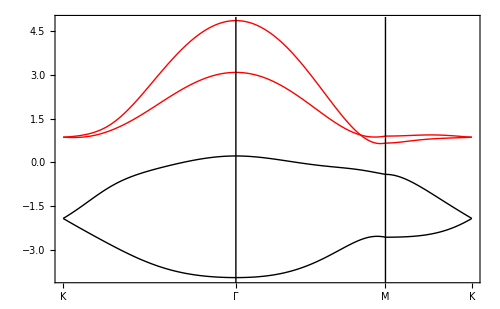

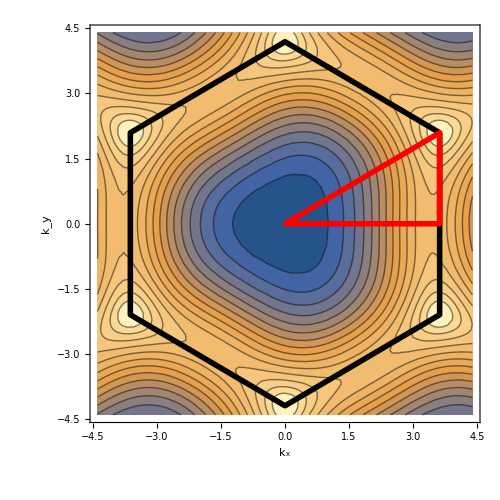

```mathematica
EVS2[kx_,ky_]:=Sort[Eigenvalues[HamFull[kx,ky]/.{t2->0.6,Δ->0,w1->0.6,w2->-0.5,α2->0.3π,t3->0.1,α3->0.6π,θw->0}]]

Δk=0.2;

Len1=Norm[Γp-Kp];
Len2=Norm[Mp-Γp];
Len3=Norm[Kp-Mp];

Ls=Table[Join[Table[{t Len1,Chop[EVS2[(Kp+(Γp-Kp)*t)[[1]],(Kp+(Γp-Kp)*t)[[2]]][[band]]]},{t,0,1,0.01}],Table[{Len1+t Len2,Chop[EVS2[(Γp+(Mp-Γp)*t)[[1]],(Γp+(Mp-Γp)*t)[[2]]][[band]]]},{t,0,1,0.01}],Table[{Len1+Len2+t Len3,Chop[EVS2[(Mp+(Kp-Mp)*t)[[1]],(Mp+(Kp-Mp)*t)[[2]]][[band]]]},{t,0,1,0.01}]],{band,1,4}];

P2=Show[ListPlot[Ls,PlotMarkers->None,Joined->True,PlotStyle->{Directive[Thick,Black],Directive[Thick,Black],Directive[Thick,Red],Directive[Thick,Red]},Frame->True,FrameStyle->Thick,ImageSize->500,FrameTicksStyle->32,FrameTicks->{{Automatic,None},{{{0,"K"},{Len1,"Γ"},{Len1+Len2,"M"},{Len1+Len2+Len3,"K"}},None}}],Graphics[{Line[{{Len1,-5},{Len1,5}}],Line[{{Len1+Len2,-5},{Len1+Len2,5}}]}]]

BAND=1;
Scl=1.4;
P1=Show[ContourPlot[EVS2[kx,ky][[BAND]],{kx,-Scl π,Scl π},{ky,-Scl π,Scl π},PlotRange->Full,Contours->15,PlotPoints->10,FrameStyle->Thick,FrameTicksStyle->32,FrameLabel->{"k_x","k_y"},LabelStyle->32,ImageSize->500],Graphics[{Thickness[0.008],Line[Table[RotationMatrix[n π/3].C1,{n,0,6}]],Red,PointSize[Large],Point[{Γp,Mp,Kp}],Thickness[0.008],Line[{Γp,Mp,Kp,Γp}]}]]
```

I guess eventually we can think about finding a way to push the additional bands further up in energy. Haven’t investigated this in too much detail yet, but will look into it.

### Spectrum of the full model: without obstruction (corresponds to a hypothetical TBG, with Dirac cones of zero net chirality)

Here we have: t2=0.

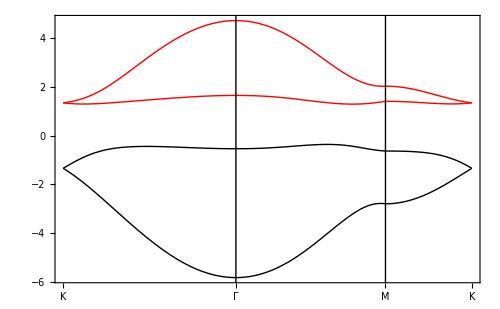

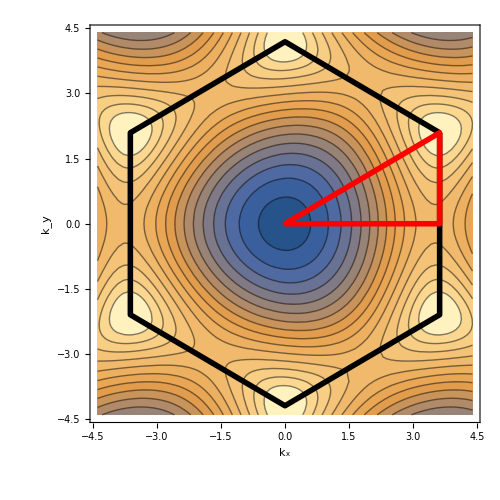

```mathematica
EVS2[kx_,ky_]:=Sort[Eigenvalues[HamFull[kx,ky]/.{t2->0,Δ->1.2,w1->0.6,w2->-0.7,α2->0.3π,t3->0.1,α3->0.6π,θw->0}]]

Δk=0.2;

Len1=Norm[Γp-Kp];
Len2=Norm[Mp-Γp];
Len3=Norm[Kp-Mp];

Ls=Table[Join[Table[{t Len1,Chop[EVS2[(Kp+(Γp-Kp)*t)[[1]],(Kp+(Γp-Kp)*t)[[2]]][[band]]]},{t,0,1,0.01}],Table[{Len1+t Len2,Chop[EVS2[(Γp+(Mp-Γp)*t)[[1]],(Γp+(Mp-Γp)*t)[[2]]][[band]]]},{t,0,1,0.01}],Table[{Len1+Len2+t Len3,Chop[EVS2[(Mp+(Kp-Mp)*t)[[1]],(Mp+(Kp-Mp)*t)[[2]]][[band]]]},{t,0,1,0.01}]],{band,1,4}];

P2=Show[ListPlot[Ls,PlotMarkers->None,Joined->True,PlotStyle->{Directive[Thick,Black],Directive[Thick,Black],Directive[Thick,Red],Directive[Thick,Red]},Frame->True,FrameStyle->Thick,ImageSize->500,FrameTicksStyle->32,FrameTicks->{{Automatic,None},{{{0,"K"},{Len1,"Γ"},{Len1+Len2,"M"},{Len1+Len2+Len3,"K"}},None}}],Graphics[{Line[{{Len1,-7},{Len1,7}}],Line[{{Len1+Len2,-7},{Len1+Len2,7}}]}]]

BAND=1;
Scl=1.4;
P1=Show[ContourPlot[EVS2[kx,ky][[BAND]],{kx,-Scl π,Scl π},{ky,-Scl π,Scl π},PlotRange->Full,Contours->15,PlotPoints->10,FrameStyle->Thick,FrameTicksStyle->32,FrameLabel->{"k_x","k_y"},LabelStyle->32,ImageSize->500],Graphics[{Thickness[0.008],Line[Table[RotationMatrix[n π/3].C1,{n,0,6}]],Red,PointSize[Large],Point[{Γp,Mp,Kp}],Thickness[0.008],Line[{Γp,Mp,Kp,Γp}]}]]
```

## Nematic order parameter

```mathematica
RotationMatrix[2π/3]//MatrixForm
```

(-1/2 | -(√3)/2
(√3)/2 | -1/2)

```mathematica
c1 = 1.5;
c2 = 0.7;
```

```mathematica
f[x_,y_]=Exp[-c1*y(y^2-3x^2)-c2(x^2+y^2)^2]
fp[x_,y_]=Exp[c1*y(y^2-3x^2)-c2(x^2+y^2)^2]
```

ⅇ^(-1.5 y (-3 x^2+y^2)-0.7 (x^2+y^2)^2)

ⅇ^(1.5 y (-3 x^2+y^2)-0.7 (x^2+y^2)^2)

```mathematica
Scl=1.0
```

1.

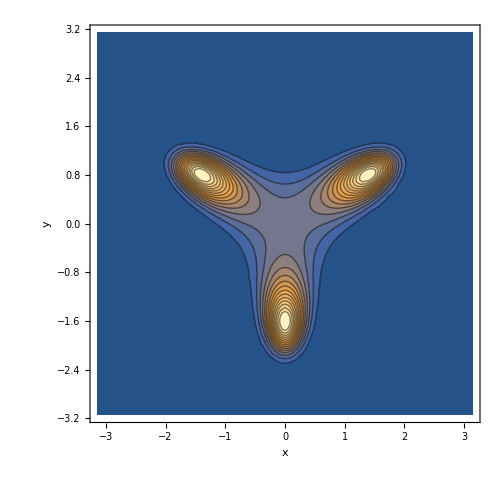

```mathematica
P1=Show[ContourPlot[f[kx,ky],{kx,-Scl* π, Scl*π},{ky,-Scl* π,Scl* π},PlotRange->Full,Contours->15,PlotPoints->10,FrameStyle->Thick,FrameTicksStyle->32,FrameLabel->{"x","y"},LabelStyle->32,ImageSize->500]]
```

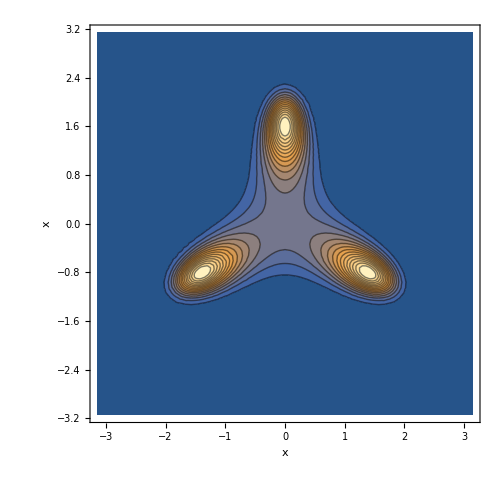

```mathematica
p2 = Show[ContourPlot[fp[kx,ky],{kx,-Scl* π, Scl*π},{ky,-Scl* π,Scl* π},PlotRange->Full,Contours->15,PlotPoints->10,FrameStyle->Thick,FrameTicksStyle->32,FrameLabel->{"x","x"},LabelStyle->32,ImageSize->500]]
```